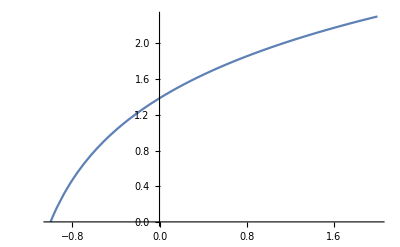

Definitionsbereich:

Reell:x>-4/3

Komplex:4+3 x≠0

Wertebereich:

Reell:True

Nullstellen:

{{x→-1}}

Beschränktheit/Limes:

Limes unendlich: ∞

Limes 0: Log[4]

Limes minus unendlich: ∞

Ableitungen:

3/(4+3 x)

-9/(4+3 x)^2

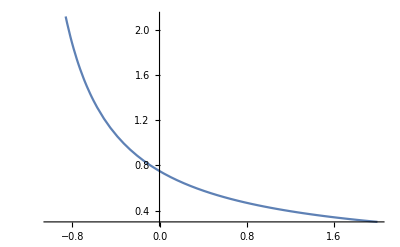

Inverse Funktion

{{x→1/3 (-4+ⅇ^y)}}

```mathematica
func = Log[3x+4];
von = -1;
bis = 2;
Plot[func, {x,von,bis}]
Print["Definitionsbereich:"]
Print["Reell:",FunctionDomain[func, x, Reals]]
Print["Komplex:",FunctionDomain[func, x, Complexes]]
Print["Wertebereich:"]
Print["Reell:",FunctionRange[func, x, y]]
Print["Nullstellen:"]
Solve[func == 0,x]
Print["Beschränktheit/Limes:"]
Print["Limes unendlich: ",Limit[func, x-> Infinity]]
Print["Limes 0: ",Limit[func, x-> 0]]
Print["Limes minus unendlich: ", Limit[func, x-> -Infinity]] 
Print["Ableitungen:"]
erste =D[func, x]
zweite = D[erste,x]
Show[Plot[erste, {x,von,bis}], Plot[zweite, {x,von,bis}]]
Print["Inverse Funktion"]
inv = Solve[y==func,x, Reals];
Print[Simplify[inv]]
```